```mathematica
ClearAll["Global`*"]
```

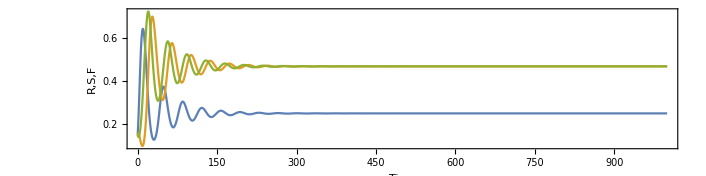

```mathematica
MetapopDyn[a_,λ_,η_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(X[t]+ Y[t] )*R[t]*η,
X'[t] ==η*(1-R[t])*Y[t] - η* R[t]*X[t] - μ*X[t],
Y'[t] ==λ*Y[t]-η*(1-R[t])*Y[t] +η* R[t] * X[t],
R[0]==0.15,X[0]==0.15,Y[0]==0.15},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=0.5,λ=0.2,η=0.4,μ=0.2,T=1000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,η,μ,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,S,F"}]
]
```

A version without the starving class...

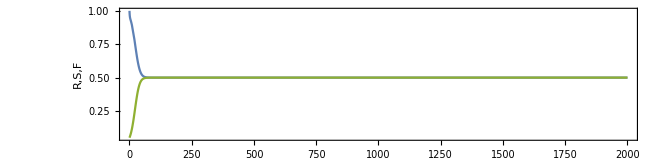

```mathematica
MetapopDyn[a_,λ_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -( Y[t])*R[t] ,
Y'[t] ==λ*Y[t]*R[t]- μ*Y[t](1-R[t]),
R[0]==1,Y[0]==0.05},{R,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=1,λ=0.1,μ=0.1,T=2000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,μ,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,S,F"}]
]
```

The below code solves for the steady state

```mathematica
Sol =FullSimplify[Solve[{
0 == α*R*(1-R)-R*(X+Y)*η,
0==η*(1-R)*Y-η*R*X-μ*X, 
0==λ*Y-η*(1-R)*Y+η*R*X},
{R,X,Y}]]
```

{{R→0,X→0,Y→0},{R→1,X→0,Y→0},{R→((η-λ) μ)/(η (λ+μ)),X→(α λ^2 (η+μ))/(η^2 (λ+μ)^2),Y→(α λ μ (η+μ))/(η^2 (λ+μ)^2)}}

```mathematica
InternalSol1 = Sol[[3]];
(*InternalSol2 = Sol[[4]];*)
```

```mathematica
{InternalSol1}/.{α->0.5,λ->0.1,μ->0.2,η->0.5}
```

{{R→0.533333,X→0.0777778,Y→0.155556}}

This means only InternalSol2 is an INTERNAL, POSITIVE SOLUTION

```mathematica
IntPosSol = InternalSol1;
```

```mathematica
Rstar = IntPosSol[[1]][[2]]
Xstar = IntPosSol[[2]][[2]]
Ystar = IntPosSol[[3]][[2]]
```

((η-λ) μ)/(η (λ+μ))

(α λ^2 (η+μ))/(η (λ+μ)^2)

(α λ μ (η+μ))/(η (λ+μ)^2)

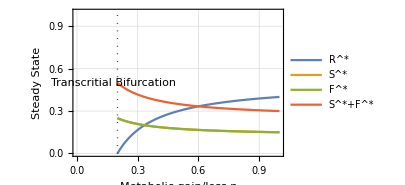

```mathematica
With[{alpha=0.5,lambda=0.2,mu=0.2},
Rstarspec = IntPosSol[[1]][[2]]/.{α->alpha,λ->lambda,μ->mu};
Xstarspec = IntPosSol[[2]][[2]]/.{α->alpha,λ->lambda,μ->mu};
Ystarspec = IntPosSol[[3]][[2]]/.{α->alpha,λ->lambda,μ->mu};
FigFP=
Show[{
Plot[{Rstarspec,Xstarspec,Ystarspec,Xstarspec+Ystarspec},{η,lambda,1},PlotTheme->"Detailed",FrameLabel->{"Metabolic gain/loss η","Steady State"},PlotRange->{{0,1},{0,1}},ImageSize->300,PlotLegends->{"R^*","S^*","F^*","S^*+F^*"}],
Graphics[{Dotted,Line[{{lambda,0},{lambda,1}}]}],
Graphics[Rotate[Text["Transcritial Bifurcation",{(lambda-0.02),0.5}],90Degree]]
}]
]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_FP_eta.pdf",FigFP]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_FP_eta.pdf

```mathematica
Limit[{Rstarspec,Xstarspec,Ystarspec},η->Infinity]
```

{0.666667,0.0555556,0.111111}

```mathematica
dR=   α*R*(1-R)-R*(X+Y);
dX =η*(1-R)*Y-η*R*X-μ*X;
dY =λ*Y-η*(1-R)*Y+η*R*X;
JacSpec = {
{D[dR,R],D[dR,X],D[dR,Y]},
{D[dX,R],D[dX,X],D[dX,Y]},
{D[dY,R],D[dY,X],D[dY,Y]}
}
```

{{-X-Y+(1-R) α-R α,-R,-R},{-X η-Y η,-R η-μ,(1-R) η},{X η+Y η,R η,-(1-R) η+λ}}

```mathematica
JacSpec//MatrixForm
```

(-X-Y+(1-R) α-R α | -R | -R
-X η-Y η | -R η-μ | (1-R) η
X η+Y η | R η | -(1-R) η+λ)

```mathematica
JacSpecSol = JacSpec/.{R->Rstar,X->Xstar,Y->Ystar};
```

```mathematica
JacSpecSol
```

{{-(α λ^2 (η+μ))/(η (λ+μ)^2)-(α λ μ (η+μ))/(η (λ+μ)^2)-(α (η-λ) μ)/(η (λ+μ))+α (1-((η-λ) μ)/(η (λ+μ))),-((η-λ) μ)/(η (λ+μ)),-((η-λ) μ)/(η (λ+μ))},{-(α λ^2 (η+μ))/(λ+μ)^2-(α λ μ (η+μ))/(λ+μ)^2,-μ-((η-λ) μ)/(λ+μ),η (1-((η-λ) μ)/(η (λ+μ)))},{(α λ^2 (η+μ))/(λ+μ)^2+(α λ μ (η+μ))/(λ+μ)^2,((η-λ) μ)/(λ+μ),λ-η (1-((η-λ) μ)/(η (λ+μ)))}}

```mathematica
({R,X,Y}/.Sol)/.{α->alpha,λ->lambda,μ->mu,η->eta}
```

{{0,0,0},{1,0,0},{((eta-lambda) mu)/(eta (lambda+mu)),(alpha lambda^2 (eta+mu))/(eta (lambda+mu)^2),(alpha lambda mu (eta+mu))/(eta (lambda+mu)^2)}}

This plot shows that the bifurcation at lambda=sigma is a Transcritical (I think)

```mathematica
Jac2=JacSpec/.Sol[[2]]
```

{{-α,-1,-1},{0,-μ-ρ,0},{0,ρ,λ}}

```mathematica
Manipulate[
Eig = Eigenvalues[JacSpecSol/.{α->0.5,λ->0.1,μ->0.2,η->eta}];
REig = Re[Eig];
IEig = Im[Eig];
Row[{
Show[{
ListPlot[Transpose[{REig,IEig}],PlotRange->{{-1,1},{-1,1}}],
Graphics[{LightGray,Opacity[0.3],Disk[]}]
},ImageSize->300,Frame->True,AspectRatio->1,FrameLabel->{"Real part","Imaginary part"}],
FP=({R,X,Y}/.Sol)/.{α->0.5,λ->0.1,μ->0.2,η->eta};
Show[{
ListPointPlot3D[FP,
PlotStyle->Directive[{ColorData[97,4],PointSize[Large]}],PlotLabel->FP,PlotRange->{{-1,1},{0,1},{0,1}},ImageSize->300,AxesLabel->{"R^*","S^*","F^*"}],
Graphics3D[{Opacity[0.5],Polygon[{{0,0,0},{0,1,0},{0,1,1},{0,0,1}}]}]
}]
}],
{{eta,0.1},0,0.2,0.001}]
```

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[List[GrayLevel[0.85`], Opacity[0.3`], DiskBox[List[0, 0]]]]}, ImageSize → 300, Frame → True, AspectRatio → 1, FrameLabel → {.

ReplaceAll::reps: {Sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListPointPlot3D::arrayerr: {R, X, Y}/. Sol must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D :: arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPointPlot3D[{R, X, Y}/. Sol, PlotStyle → Directive[{InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[0.922526, 0.385626, 0.209179], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.615017, 0.257084, 0.139453]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35, CurrentValue["FontCapHeight"], Power[AbsoluteCurrentValue[Magnification], -1]]]]]] , "RGBColor[0.922526, 0.385626, 0.209179]"], Rule[Appearance, None], Rule[BaseStyle, List[]], Rule[BaselinePosition, Baseline], Rule[DefaultBaseStyle, List[]], RuleDelayed[ButtonFunction, With[List[Set[Typeset`box$, EvaluationBox[]]], If[Not[AbsoluteCurrentValue["Deployed"]], CompoundExpression[SelectionMove[Typeset`box$, All, Expression], Set[FrontEnd`Private`$ColorSelectorInitialAlpha, 1], Set[FrontEnd`Private`$ColorSelectorInitialColor, RGBColor[0.922526, 0.385626, 0.209179]], Set[FrontEnd`Private`$ColorSelectorUseMakeBoxes, True], MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], List[0, List[Left, Bottom]], List[Left, Top], Rule["ClosingActions", List["SelectionDeparture", "ParentChanged", "EvaluatorQuit"]]]]]]]], Rule[BaseStyle, Inherited], Rule[Evaluator, Automatic], Rule[Method, "Preemptive"]], RGBColor[0.922526, 0.385626, 0.209179], Rule[Editable, False], Rule[Selectable, False]], PointSize[Large]}], PlotLabel → ({R, X, Y}/. Sol), PlotRange → {{-1, 1}, {0, 1}, {0, 1}}, ImageSize → 300, AxesLabel → {"\!\(\*SuperscriptBox[\(R\), \(*\)]\)", "\!\(\*SuperscriptBox[\(S\), \(*\)]\)", "\!\(\*SuperscriptBox[\(F\), \(*\)]\)"}], Graphics3DBox[List[Opacity[0.5], Polygon3DBox[List[List[0, 0, 0], List[0, 1, 0], List[0, 1, 1], List[0, 0, 1]]]]]}].

General::stop: Further output of Show :: gcomb will be suppressed during this calculation.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[List[GrayLevel[0.85`], Opacity[0.3`], DiskBox[List[0, 0]]]]}, ImageSize → 300, Frame → True, AspectRatio → 1, FrameLabel → {.

ReplaceAll::reps: {Sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListPointPlot3D::arrayerr: {R, X, Y}/. Sol must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D :: arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPointPlot3D[{R, X, Y}/. Sol, PlotStyle → Directive[{InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[0.922526, 0.385626, 0.209179], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.615017, 0.257084, 0.139453]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35, CurrentValue["FontCapHeight"], Power[AbsoluteCurrentValue[Magnification], -1]]]]]] , "RGBColor[0.922526, 0.385626, 0.209179]"], Rule[Appearance, None], Rule[BaseStyle, List[]], Rule[BaselinePosition, Baseline], Rule[DefaultBaseStyle, List[]], RuleDelayed[ButtonFunction, With[List[Set[Typeset`box$, EvaluationBox[]]], If[Not[AbsoluteCurrentValue["Deployed"]], CompoundExpression[SelectionMove[Typeset`box$, All, Expression], Set[FrontEnd`Private`$ColorSelectorInitialAlpha, 1], Set[FrontEnd`Private`$ColorSelectorInitialColor, RGBColor[0.922526, 0.385626, 0.209179]], Set[FrontEnd`Private`$ColorSelectorUseMakeBoxes, True], MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], List[0, List[Left, Bottom]], List[Left, Top], Rule["ClosingActions", List["SelectionDeparture", "ParentChanged", "EvaluatorQuit"]]]]]]]], Rule[BaseStyle, Inherited], Rule[Evaluator, Automatic], Rule[Method, "Preemptive"]], RGBColor[0.922526, 0.385626, 0.209179], Rule[Editable, False], Rule[Selectable, False]], PointSize[Large]}], PlotLabel → ({R, X, Y}/. Sol), PlotRange → {{-1, 1}, {0, 1}, {0, 1}}, ImageSize → 300, AxesLabel → {"\!\(\*SuperscriptBox[\(R\), \(*\)]\)", "\!\(\*SuperscriptBox[\(S\), \(*\)]\)", "\!\(\*SuperscriptBox[\(F\), \(*\)]\)"}], Graphics3DBox[List[Opacity[0.5], Polygon3DBox[List[List[0, 0, 0], List[0, 1, 0], List[0, 1, 1], List[0, 0, 1]]]]]}].

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol]], Im[Eigenvalues[JacSpecSol]]}], PlotRange → {{-1, 1}, {-1, 1}}], GraphicsBox[List[GrayLevel[0.85`], Opacity[0.3`], DiskBox[List[0, 0]]]]}, ImageSize → 300, Frame → True, AspectRatio → 1, FrameLabel → {.

ReplaceAll::reps: {Sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListPointPlot3D::arrayerr: {R, X, Y}/. Sol must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D :: arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPointPlot3D[{R, X, Y}/. Sol, PlotStyle → Directive[{InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[0.922526, 0.385626, 0.209179], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.615017, 0.257084, 0.139453]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35, CurrentValue["FontCapHeight"], Power[AbsoluteCurrentValue[Magnification], -1]]]]]] , "RGBColor[0.922526, 0.385626, 0.209179]"], Rule[Appearance, None], Rule[BaseStyle, List[]], Rule[BaselinePosition, Baseline], Rule[DefaultBaseStyle, List[]], RuleDelayed[ButtonFunction, With[List[Set[Typeset`box$, EvaluationBox[]]], If[Not[AbsoluteCurrentValue["Deployed"]], CompoundExpression[SelectionMove[Typeset`box$, All, Expression], Set[FrontEnd`Private`$ColorSelectorInitialAlpha, 1], Set[FrontEnd`Private`$ColorSelectorInitialColor, RGBColor[0.922526, 0.385626, 0.209179]], Set[FrontEnd`Private`$ColorSelectorUseMakeBoxes, True], MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], List[0, List[Left, Bottom]], List[Left, Top], Rule["ClosingActions", List["SelectionDeparture", "ParentChanged", "EvaluatorQuit"]]]]]]]], Rule[BaseStyle, Inherited], Rule[Evaluator, Automatic], Rule[Method, "Preemptive"]], RGBColor[0.922526, 0.385626, 0.209179], Rule[Editable, False], Rule[Selectable, False]], PointSize[Large]}], PlotLabel → ({R, X, Y}/. Sol), PlotRange → {{-1, 1}, {0, 1}, {0, 1}}, ImageSize → 300, AxesLabel → {"\!\(\*SuperscriptBox[\(R\), \(*\)]\)", "\!\(\*SuperscriptBox[\(S\), \(*\)]\)", "\!\(\*SuperscriptBox[\(F\), \(*\)]\)"}], Graphics3DBox[List[Opacity[0.5], Polygon3DBox[List[List[0, 0, 0], List[0, 1, 0], List[0, 1, 1], List[0, 0, 1]]]]]}].

```mathematica
FP
```

{{0,0,0},{1,0,0},{0.,0.166667,0.333333}}

Specific Bifurcations

```mathematica
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,η]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,μ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,α]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,λ]
```

{{η→λ},{η→-μ}}

{{μ→0},{μ→-η}}

{{α→0}}

{{λ→0},{λ→η}}

```mathematica
SylvesterMatrix=Function[{Jac},
Dim = Length[Jac];
Mat = Table[0,{Dim-1},{Dim-1}];
Col1 = Table[Subscript[ℼ,i],{i,1,(Dim-1)*2,2}];
Mat[[All,1]] = Col1;
Table[
Mat[[i]][[j]] = Subscript[ℼ,Mat[[i]][[j-1]][[2]]-1];
,{j,2,Dim-1},{i,1,Dim-1,1}];
Todel=Select[Flatten[Mat],#[[2]]<0||#[[2]]>(Dim)&];
Mat=Mat/.Table[Todel[[i]]->0,{i,1,Length[Todel],1}];
CPG = FullSimplify[CharacteristicPolynomial[Jac,λ]];
CPGL = CoefficientList[CPG,λ];
Mat2 = Mat/.Table[Subscript[ℼ,i]-> CPGL[[i+1]],{i,0,(Length[CPGL]-1),1}]
];
```

```mathematica
Sylv=SylvesterMatrix[JacSpecSol];
HopfSol=Solve[Det[Sylv]==0,muy];
```

$Aborted

```mathematica
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
```

```mathematica
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
```

```mathematica
HopfAnalytic = Solve[Det[Sylv]==0,λ];
```

```mathematica
HopfAnalytic
```

{{λ→η},{λ→-(-3 η^2+α μ-2 η μ)/(3 η)-(2^(1/3) (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2))/(3 η (27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3+√(4 (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2)^3+(27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3)^2))^(1/3))+1/(3 2^(1/3) η)(27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3+√(4 (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2)^3+(27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3)^2))^(1/3)},{λ→-(-3 η^2+α μ-2 η μ)/(3 η)+((1+ⅈ √3) (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2))/(3 2^(2/3) η (27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3+√(4 (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2)^3+(27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3)^2))^(1/3))-1/(6 2^(1/3) η)(1-ⅈ √3) (27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3+√(4 (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2)^3+(27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3)^2))^(1/3)},{λ→-(-3 η^2+α μ-2 η μ)/(3 η)+((1-ⅈ √3) (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2))/(3 2^(2/3) η (27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3+√(4 (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2)^3+(27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3)^2))^(1/3))-1/(6 2^(1/3) η)(1+ⅈ √3) (27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3+√(4 (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2)^3+(27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3)^2))^(1/3)}}

```mathematica
FullSimplify[HopfAnalytic]
```

$Aborted

```mathematica
HopfAnalytic[[2]]
```

{λ→-(-3 η^2+α μ-2 η μ)/(3 η)-(2^(1/3) (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2))/(3 η (27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3+√(4 (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2)^3+(27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3)^2))^(1/3))+1/(3 2^(1/3) η)(27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3+√(4 (-6 η^4-15 η^3 μ-α^2 μ^2+α η μ^2-10 η^2 μ^2)^3+(27 η^6-18 α η^4 μ+90 η^5 μ-45 α η^3 μ^2+90 η^4 μ^2-2 α^3 μ^3+3 α^2 η μ^3-24 α η^2 μ^3+25 η^3 μ^3)^2))^(1/3)}

The solution to the Hopf Bifurcation surface may not be analytically tractable
Try Solving numerically with a = 1

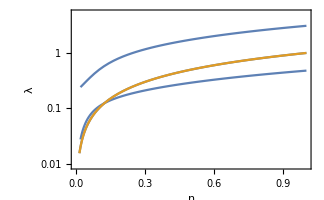

```mathematica
Hsp = HopfAnalytic/.{α->0.5,μ->0.2};
LogPlot[{λ/.Hsp,η},{η,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{"η","λ"},PlotStyle->ColorData[97]]
```

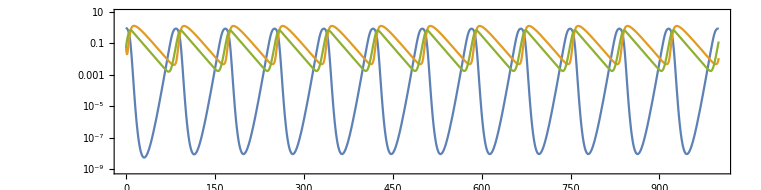

```mathematica
MetapopDyn[a_,λ_,η_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(X[t] + Y[t])*R[t] ,
X'[t] ==η*(1-R[t])*Y[t] - η* R[t]*X[t] - μ*X[t],
Y'[t] ==λ*Y[t]-η*(1-R[t])*Y[t] +η* R[t] * X[t],
R[0]==1,X[0]==0.05,Y[0]==0.05},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=0.5,η=0.6,λ=0.5,μ=0.2,T=1000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,η,μ,T] ];
LogPlot[Traj,{t,0,T},PlotRange->{0,1},AspectRatio->0.25,Frame->True]
]
```

```mathematica
Hsp2 =HopfAnalytic/.{α->0.5};
Plot3D[{η,λ/.Hsp2[[4]]},{η,0,1},{μ,0,1},PlotRange->{0,1}, ClippingStyle->None,PlotStyle->{Directive[ColorData[97,1],Opacity[0.8]],Directive[ColorData[97,2],Opacity[0.8]]},Mesh->None,AxesLabel->{"η","μ","λ"},PlotLegends->{"SN","Hopf"},Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
HopfData = Table[{σ,Re[N[λ/.Hsp[[4]]]]},{σ,0.1,1,0.01}];
(*HopfData=Join[{Reverse[HopfNumSol2down,2]/.σ->"NA",Reverse[HopfNumSol2up,2]/.σ->"NA"}];*)
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfData.csv",HopfData,"CSV"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfData.csv

```mathematica
RandomReal[{0.001,1000}]
```

65.4148

```mathematica
Remove[b]
```

```mathematica
SppData = Table[
B0 = RandomReal[];
Bm = RandomReal[];
m0 = RandomReal[{0.001,1000}];
β=0.75;
ϵ=RandomReal[{1,10}];
md = ϵ*m0;
b = 600;
a = B0/Bm*b;
{η*(1 - b/a*md^(1-β)),Log[md/m0]/(1/(b*(1-β))*Log[(1 - b/a*m0^(1-β))/(1 - b/a*md^(1-β))])},{}]
```

Table::itform: Argument {} at position 2 does not have the correct form for an iterator.

Table[B0=RandomReal[];Bm=RandomReal[];m0=RandomReal[{0.001,1000}];β=0.75;ϵ=RandomReal[{1,10}];md=ϵ m0;b=600;a=(B0 b)/Bm;{η (1-(b md^(1-β))/a),Log[md/m0]/(Log[(1-(b m0^(1-β))/a)/(1-(b md^(1-β))/a)]/(b (1-β)))},{}]

Power::infy: Infinite expression 1/0. encountered.

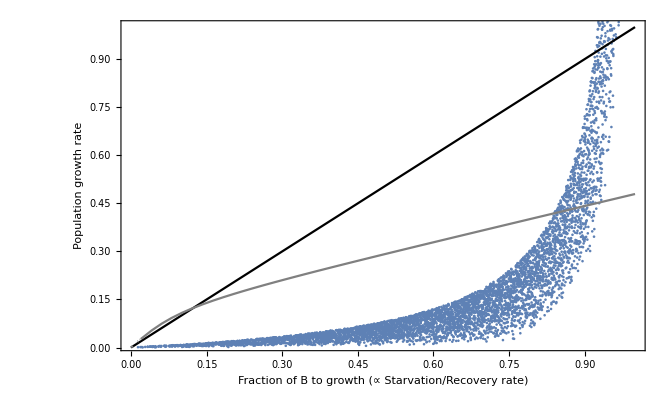

```mathematica
SppData = Table[
β=RandomReal[{0.5,1}];
(*b = RandomReal[{0.000001,0.00001}];*)
b = 0.08; (*RandomReal[{0.00002,1}];*)
ϵ=RandomReal[{1,20}];
γ0 = x;
η = 1;
{η*γ0,N[ Log[ϵ]/(1/(b*(1-β))*Log[γ0/(1-ϵ^(1-β)*(1-γ0))])]},
{x,0.0001,1,0.0001}];
Colors = {Black,Transparent,Transparent,Gray};
Show[{
ListPlot[SppData,PlotRange->{{0,1},{0.01,1}},Frame->True,FrameLabel->{"Fraction of B to growth (∝ Starvation/Recovery rate)","Population growth rate"},PlotStyle->ColorData[97,1]],
Table[Plot[λ/.Hsp[[x]],{η,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{"η","λ"},PlotStyle->Colors[[x]]],{x,1,4}]
}]
```

```mathematica
Colors[[1]]
```

Black

```mathematica
Table[{λ/.Hsp[[x]]},{x,1,4}]
```

{{η},{-(0.1-0.4 η-3 η^2)/(3 η)-(2^(1/3) (-0.01+0.02 η-0.4 η^2-3. η^3-6 η^4))/(3 η (-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6+√(4 (-0.01+0.02 η-0.4 η^2-3. η^3-6 η^4)^3+(-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6)^2))^(1/3))+1/(3 2^(1/3) η)(-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6+√(4 (-0.01+0.02 η-0.4 η^2-3. η^3-6 η^4)^3+(-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6)^2))^(1/3)},{-(0.1-0.4 η-3 η^2)/(3 η)+((1+ⅈ √3) (-0.01+0.02 η-0.4 η^2-3. η^3-6 η^4))/(3 2^(2/3) η (-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6+√(4 (-0.01+0.02 η-0.4 η^2-3. η^3-6 η^4)^3+(-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6)^2))^(1/3))-1/(6 2^(1/3) η)(1-ⅈ √3) (-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6+√(4 (-0.01+0.02 η-0.4 η^2-3. η^3-6 η^4)^3+(-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6)^2))^(1/3)},{-(0.1-0.4 η-3 η^2)/(3 η)+((1-ⅈ √3) (-0.01+0.02 η-0.4 η^2-3. η^3-6 η^4))/(3 2^(2/3) η (-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6+√(4 (-0.01+0.02 η-0.4 η^2-3. η^3-6 η^4)^3+(-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6)^2))^(1/3))-1/(6 2^(1/3) η)(1+ⅈ √3) (-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6+√(4 (-0.01+0.02 η-0.4 η^2-3. η^3-6 η^4)^3+(-0.002+0.006 η-0.096 η^2-0.7 η^3+1.8 η^4+18. η^5+27 η^6)^2))^(1/3)}}